## MRAC for unstable 1st-order system with unknown rate Problem 10.3

System structure is G_0(s) = 1/(s-a)   with a unknown and possible unstable (a>0)
used for book, Adaptive Control chapter;    Lyapunov algorithm

```mathematica
Clear["Global`*"];
(* SetOptions[Plot,PlotRange -> All,Background->GrayLevel[0.97],PlotStyle->Thick]; *)
```

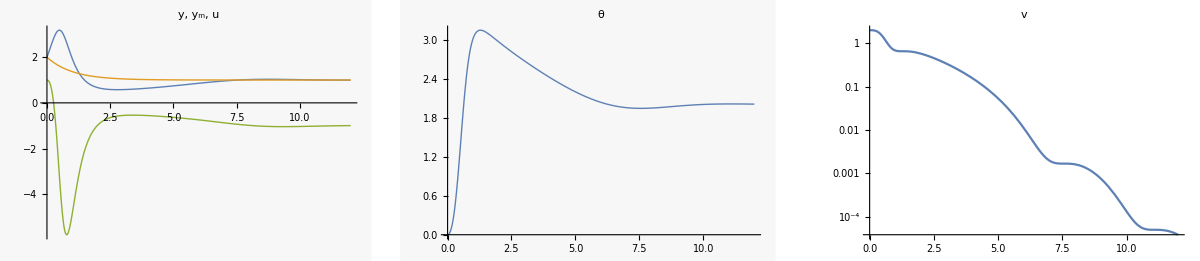

```mathematica
tend=12;
uc[t_]:= uc0  ;      (* reference input *)
e[t]=y[t]-ym[t]; (* error between sys & model *)
θstar=a-am;  (* parameter estimate error *)

eqs={
y'[t]== a y[t]+u[t] + 0*DiracDelta[t-10],
ym'[t]== am ym[t]+uc[t],
θ'[t]==γ  y[t]e[t],(* derived from Lyapunov function *)
u[t]== uc[t] - θ[t]y[t],
v[t]==1/2(e[t]^2+1/γ(θ[t]-θstar)^2)};  
init={y[0]==y0,ym[0]==ym0,θ[0]==θ0};
pars={γ->1,a->1,am->-1,uc0->1,y0->2,ym0->2,θ0->0};

{ys,yms,θs,us,vs}=NDSolveValue[{eqs,init}/.pars,
{y,ym,θ,u,v},{t,0,tend},MaxSteps->10^5];
p1=Plot[{ys[t],yms[t],us[t]},{t,0,tend},PlotRange->All,PlotLabel->"y, y_m, u"];
p2=Plot[θs[t],{t,0,tend},PlotLabel->"θ",PlotRange->All];
p3=LogPlot[vs[t],{t,0,tend},PlotLabel->"v",PlotRange->All];
GraphicsRow[{p1,p2,p3},ImageSize->Full]
```

explore uc=0 case analytically

```mathematica
θanalytic=DSolveValue[{θ'[t]+θ[t]^2==γ y0^2,θ[0]==0},θ[t],t]
```

y0 √γ Tanh[t y0 √γ]

```mathematica
yanalytic=DSolveValue[{y'[t]+ y[t]θanalytic==0,y[0]==y0},y[t],t]//FullSimplify
```

y0 Sech[t y0 √γ]

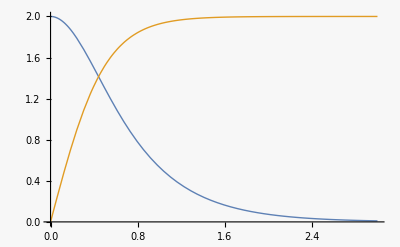

```mathematica
Plot[{yanalytic/.pars,θanalytic/.pars},{t,0,3}]
```

Export data

```mathematica
dt=0.1;dat=Table[{ys[t],yms[t],us[t],θs[t],vs[t]},{t,0,tend,dt}];
(* 
SetDirectory[NotebookDirectory[]];Export["mrac1stOrderUnknownRate_data.dat",dat]; 
*)
```